```mathematica
SensorLinB1r[g_] := Module[{mmIni,mmIniPairs,gn1,nodesp, nodesn,temp,temp2, gbipartite,maxmatching, gml,  NumberOfNodes, sensors, sensorswhere, sensorslin},
mmIni =FindIndependentEdgeSet[Graph[RandomSample[EdgeList[g]]]];
mmIniPairs=Partition[mmIni,1]/.{x_-> y_}->{x,y};
gn1 = EdgeDelete[g,mmIni];
nodesp=ToString[#]<>"p"&/@VertexList[gn1]; 
nodesn=ToString[#]<>"n"&/@VertexList[gn1];
(* create edges for the bipartite graph, e.g., 1->2 corresponds to 1p <-> 1n *)
temp=Partition[EdgeList[gn1],1]/.{x_-> y_}->{x,y} ;
temp2={ToString[#[[1]]]<>"p",ToString[#[[2]]]<>"n"}&/@temp;
gbipartite=Graph[Join[Join[RandomSample[nodesp], RandomSample[nodesn]]],Flatten[temp2/.{x_,y_}->{x<->y}] , VertexLabels->"Name", GraphLayout->"BipartiteEmbedding"]; 
maxmatching=FindIndependentEdgeSet[gbipartite];
gml=VertexList[Graph[maxmatching]];
NumberOfNodes=VertexCount[gn1];sensorswhere=Table[FreeQ[gml,ToString[i]<>"p" ],{i,1,NumberOfNodes}];sensorslin=Flatten[Position[sensorswhere,True]];
sensors = If[Length[sensorslin]==0, RandomInteger[{1,NumberOfNodes}],sensorslin]; 
sensors
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
parameterDir="Community_parameters/";
dataDir = "data/";
```

```mathematica
samples = 5000; (*number of MSS*)
fn = "M_SD_020"; (*WoL ID*)
```

## get data

```mathematica
A=Transpose[Import[parameterDir<>fn<>"_Abin.csv", "Table"] ];
G = DirectedGraph[AdjacencyGraph[Transpose[A]]];
speciesl= VertexList[G];
EWScore = Flatten[Import[dataDir<>fn<>"_detection100.csv", "Table"]];
EWScore0 = Flatten[Import[dataDir<>fn<>"_detection0.csv", "Table"]];
```

## calculate sensor score

```mathematica
MSS= Table[SensorLinB1r[G],{samples}]; 
SensorScore= N[Table[Length[Position[MSS, speciesl[[i]]]]/samples,{i,VertexCount[G]}]];
```

## correlation tests

```mathematica
SpearmanRankTest[EWScore,SensorScore,{"TestDataTable"}] (*with competition*)
```

{ | Statistic | P-Value
Spearman Rank | 0.721302 | 1.69387×10^-10}

## plot parameters and data

```mathematica
or2 = Ordering[SensorScore];
c2=Table[ColorData["Rainbow"][i],{i,0,1,1/(Length[or2]-1)}];
c2o=Table[c2[[Flatten[Position[or2,i]]]],{i,Length[or2]}];
animals=Position[A[[1]],_?(#>= 1&)][[1]][[1]];
vs=Table[i-> "Diamond",{i,animals}];
dataEWSS=Transpose@{10*EWScore, SensorScore};
Fitt=FindFit[dataEWSS,{a/(1+b*Exp[-c (x-d)])},{a,b,c,d},x];
FitData=Table[a/(1+b*Exp[-c (x-d)])/.Fitt,{x,0,7}];
dataEWSS0=Transpose@{10*EWScore0, SensorScore};
```

## plots

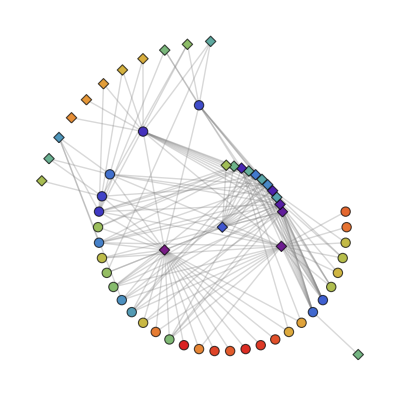

```mathematica
Gp = UndirectedGraph[AdjacencyGraph[Transpose[A]],
GraphLayout->"RadialEmbedding",
VertexStyle->Thread[Range[Length[c2o]]->c2o],
VertexSize->1.2,EdgeStyle->Opacity[0.3, Gray],
VertexShapeFunction->vs]
```

```mathematica
BarLegend[{"Rainbow",{Min@SensorScore,Max@SensorScore}},
LabelStyle->Directive[FontSize->13],
LegendLayout->"Row"
]
```

## EW Score vs Sensor Score

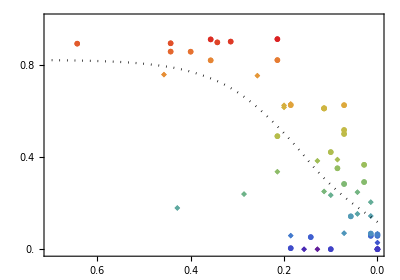

```mathematica
Show[
ListPlot[Flatten[{dataEWSS[[1;;animals]]},{2}],
PlotStyle->c2o,
Frame->True,
FrameStyle->Black,
FrameTicksStyle->12,
PlotMarkers->{◆,Large},
AspectRatio->0.7,
ImageSize->{Automatic,220},
PlotRange->{{0,7},{-0.01,1}},
ScalingFunctions->{"Reverse",Automatic},(*FrameTicks->{{{0,"0.0"},{1,"0.1"},{2,"0.2"},{3,"0.3"},{4,"0.4"},{5,"0.5"},{6,"0.6"}},Automatic}, *)
FrameTicks->{{Range[0,2,0.2],None},{{{0,"0.0"},{1,"0.1"},{2,"0.2"},{3,"0.3"},{4,"0.4"},{5,"0.5"},{6,"0.6"},{7,"0.7"}},None}}, 
AxesOrigin->{5,0}]
, 
ListPlot[Flatten[{dataEWSS[[animals+1;;Length[dataEWSS]]]},{2}],PlotStyle->c2o[[animals+1;;Length[dataRepeatS2]]],PlotMarkers->{●,Small},ScalingFunctions->{"Reverse",Automatic},AxesLabel->{"w_i","sensor score"},
Ticks->{{{2,"0.2"},{4,"0.4"},{6,"0.6"}},Automatic}]
,
ListPlot[Transpose@{Range[8]-1,FitData},Joined->True,InterpolationOrder->2,ScalingFunctions->{"Reverse",Automatic},PlotRange->{Automatic,{0,1}},PlotStyle->{Black,Dotted},AxesLabel->{"w_i","sensor score"}]
]
```

## Vertex degree vs Sensor Score

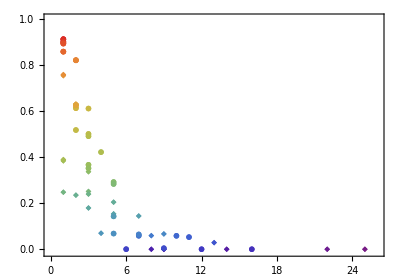

```mathematica
dataDegreedScore = Transpose@{VertexDegree[Gp],SensorScore};
Show[ListPlot[Flatten[{dataDegreedScore[[1;;animals]]},{2}],
PlotStyle->c2o,
Frame->True,
FrameStyle->Black,
FrameTicksStyle->12,
PlotMarkers->{◆,Large},
AspectRatio->0.7,
ImageSize->{Automatic,220},
PlotRange->{{-.02,26},{-0.01,1}}],
ListPlot[Flatten[{dataDegreedScore[[animals+1;;Length[dataDegreedScore]]]},{2}],PlotStyle->c2o[[animals+1;;Length[dataDegreedScore]]],PlotMarkers->{●,Small}]]
```

## Compare the EW score with and without competition

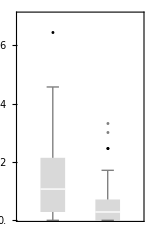

```mathematica
BoxWhiskerChart[{EWScore,EWScore0},"Outliers",
AspectRatio->GoldenRatio,
ImageSize->150,
FrameStyle->Black,
FrameTicksStyle->12,
ImageSize->{Automatic,220},
PlotRange->{Automatic,{0.01,0.7}},
FrameTicks->{{Range[0,1,0.1],None},{Range[0,1,0.2],None}},
ChartStyle->LightGray
]
```

## EW Score vs Sensor Score without competition

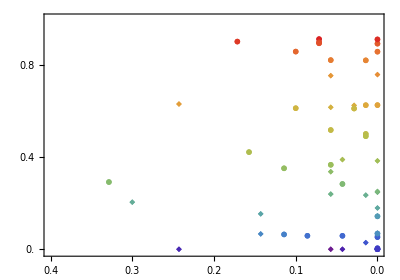

```mathematica
Show[
ListPlot[Flatten[{dataEWSS0[[1;;animals]]},{2}],
PlotStyle->c2o,
Frame->True,
FrameStyle->Black,
FrameTicksStyle->12,
PlotMarkers->{◆,Large},
AspectRatio->0.7,
ImageSize->{Automatic,220},
PlotRange->{{0,4},{-0.01,1}},
ScalingFunctions->{"Reverse",Automatic},(*FrameTicks->{{{0,"0.0"},{1,"0.1"},{2,"0.2"},{3,"0.3"},{4,"0.4"},{5,"0.5"},{6,"0.6"}},Automatic}, *)
FrameTicks->{{Range[0,2,0.2],None},{{{0,"0.0"},{1,"0.1"},{2,"0.2"},{3,"0.3"},{4,"0.4"}},None}}]
, 
ListPlot[Flatten[{dataEWSS0[[animals+1;;Length[dataEWSS0]]]},{2}],PlotStyle->c2o[[animals+1;;Length[dataRepeatS20]]],PlotMarkers->{●,Small},ScalingFunctions->{"Reverse",Automatic},AxesLabel->{"w_i","sensor score"},
Ticks->{{{2,"0.2"},{4,"0.4"},{6,"0.6"}},Automatic}]
]
```